```mathematica
<<MaTeX`
```

```mathematica
data=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi.csv"];
```

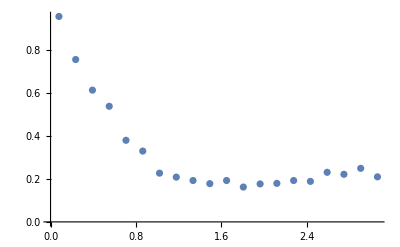

```mathematica
ListPlot[data]
```

```mathematica
Total[data[[All,2]]*ArrayPad[Differences[data[[All,1]]],{0,1},"Reversed"]]
```

1.

```mathematica
n[data_]:=Total[data[[All,2]]*ArrayPad[Differences[data[[All,1]]],{0,1},"Reversed"]]
```

## [1.0, 1.4], [1.4, 2.0], N = 1 000 000, MPI on/off

```mathematica
data1MPIon=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e6__1014_1420_mpi.csv"];
```

```mathematica
data1MPIoff=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e6__1014_1420__.csv"];
```

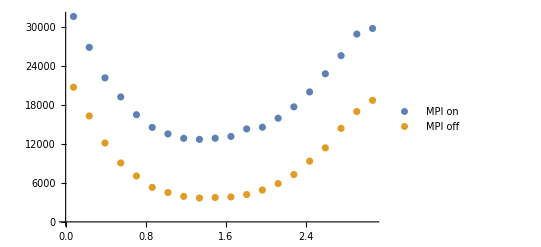

```mathematica
plot1=ListPlot[{data1MPIon, data1MPIoff},PlotLegends->{"MPI on", "MPI off"},PlotLabel->MaTeX["N=10^6, \\; p_T^1\\in [1.0, 1.4], \\; p_T^2\\in [1.4, 2.0]"]]
```

```mathematica
Export["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/corr1.pdf",plot1]
```

/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/corr1.pdf

## [1.0, 1.4], [1.4, 2.0], N = 1 000 000, MPI on/off, unity

```mathematica
data2MPIonUnity=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e6__1014_1420_mpi_unity.csv"];
```

```mathematica
data2MPIoffUnity=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e6__1014_1420__unity.csv"];
```

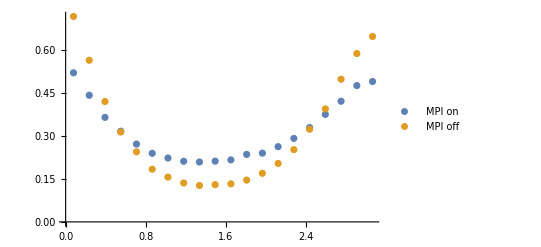

```mathematica
plot2=ListPlot[{data2MPIonUnity, data2MPIoffUnity},PlotLegends->{"MPI on", "MPI off"},PlotLabel->MaTeX["N=10^6, \\; p_T^1\\in [1.0, 1.4], \\; p_T^2\\in [1.4, 2.0], \\;\\int = 1"]]
```

```mathematica
Export["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/corr2.pdf",plot2]
```

/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/corr2.pdf

## [2.4, 2.8], [2.8, 5.0], N = 1 000 000

```mathematica
data2=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_2.csv"];
```

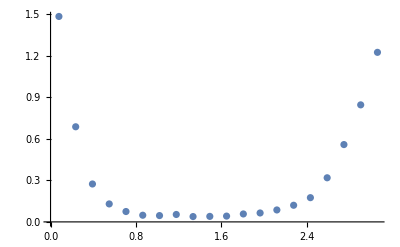

```mathematica
plot2=ListPlot[data2]
```

```mathematica
Export["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/corr2.pdf",plot2]
```

/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/corr2.pdf

## [1.0, 1.4], [1.4, 2.0], N = 10 000 000, 2.6 < η < 4.1

```mathematica
data3MPIon=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_2641_1014_1420_mpi.csv"];
```

```mathematica
data3MPIoff=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_2641_1014_1420__.csv"];
```

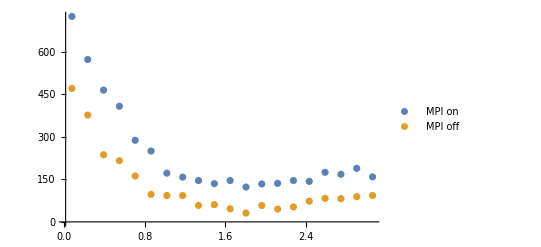

```mathematica
plot3=ListPlot[{data3MPIon, data3MPIoff},PlotLegends->{"MPI on", "MPI off"},PlotLabel->MaTeX["N=10^7, \\; p_T^1\\in [1.0, 1.4], \\; p_T^2\\in [1.4, 2.0], \\; y \\in [2.6, 4.1]"],PlotRange->All]
```

```mathematica
Export["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/corr3.pdf",plot3]
```

/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/corr3.pdf

## [1.0, 1.4], [1.4, 2.0], N = 100 000 000, 2.6 < η < 4.1

```mathematica
data4MPIon=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e8_2641_1014_1420_mpi.csv"];
```

```mathematica
data4MPIoff=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e8_2641_1014_1420__.csv"];
```

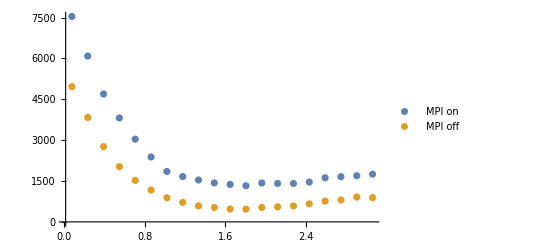

```mathematica
plot4=ListPlot[{data4MPIon,data4MPIoff},PlotLegends->{"MPI on","MPI off"},PlotLabel->MaTeX["N=10^8, \\; p_T^1\\in [1.0, 1.4], \\; p_T^2\\in [1.4, 2.0], \\; y \\in [2.6, 4.1]"],PlotRange->All]
```

```mathematica
Export["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/corr4.pdf",plot4]
```

/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/corr4.pdf

## [1.0, 1.4], [1.4, 2.0], N = 100 000 000, ensemble

```mathematica
data51=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_0010_1014_1420_mpi.csv"];
```

```mathematica
data52=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_1020_1014_1420_mpi.csv"];
```

```mathematica
data53=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_2030_1014_1420_mpi.csv"];
```

```mathematica
data54=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_3040_1014_1420_mpi.csv"];
```

```mathematica
data55=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_4050_1014_1420_mpi.csv"];
```

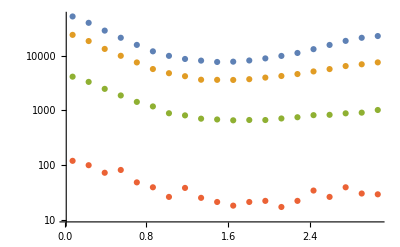

```mathematica
ListLogPlot[{data51,data52,data53,data54,data55},PlotLegends->MaTeX/@{"0.0<y<1.0","1.0<y<2.0","2.0<y<3.0","3.0<y<4.0","4.0<y<5.0"},PlotLabel->MaTeX["N=10^7, \\; p_T^1\\in [1.0, 1.4], \\; p_T^2\\in [1.4, 2.0]"],PlotRange->All]
```

## [1.0, 1.4], [1.4, 2.0], N = 100 000 000, ensemble, unity

```mathematica
data61=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_0010_1014_1420_mpi_unity.csv"];
```

```mathematica
data62=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_1020_1014_1420_mpi_unity.csv"];
```

```mathematica
data63=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_2030_1014_1420_mpi_unity.csv"];
```

```mathematica
data64=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi_1e7_3040_1014_1420_mpi_unity.csv"];
```

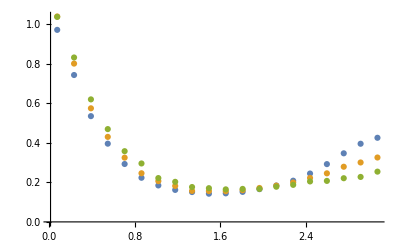

```mathematica
ListPlot[{data61,data62,data63},PlotLegends->MaTeX/@{"0.0<y<1.0","1.0<y<2.0","2.0<y<3.0","3.0<y<4.0"},PlotLabel->MaTeX["N=10^7, \\; p_T^1\\in [1.0, 1.4], \\; p_T^2\\in [1.4, 2.0], \\;\\int = 1"],PlotRange->All]
```